```mathematica
Clear["Global`*"]

(*Black hole mass = 9.3 × 10^(6) solarmass*)

α1= 3.5 × 10^(-5);
ϵ= -4.7× 10^(-8);

sol1=NDSolve[{r ϕ''[r]+2ϕ'[r]==2*r*(V[r]-ϵ-α1/r)ϕ[r],r V''[r]+2V'[r]==r ϕ[r]^2,ϕ[0.0035]== 4.3×10^(-7),ϕ'[0.0035]==-3.5×10^(-5)×4.3×10^(-7),V[0.0035]==-4.3×10^(-7), V'[0.0035]==0},{ϕ,V},{r,0.0035,4000}]
```

{{ϕ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
ϕ[0.0035]== 4.3×10^(-7)
```

ϕ[0.0035]==4.3×10^-7

```mathematica
(* r_h = √(3/ϕ[0.0035]) - 3* α1/ ϕ[0.0035] ; the definition of r_h from the paper*)

V[2400] /. sol1 (* This is V_d(r_h) for the corresponding BH mass*)
```

{-3.20259×10^-7}

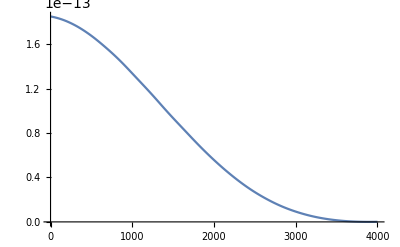

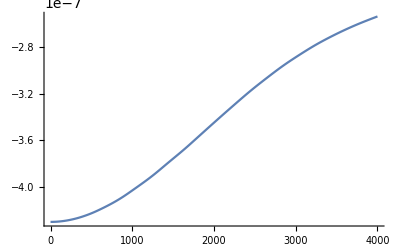

```mathematica
Plot[Evaluate[{ϕ[r]^2}/.sol1],{r,0.0035,4000},PlotRange->All, PlotPoints->200]
Plot[Evaluate[{V[r]}/.sol1],{r,0.0035,4000},PlotRange->All, PlotPoints->200]
```

```mathematica
NIntegrate[Evaluate[4*π*r^2*ϕ[r]^2  /.sol1],{r,0.0035,4000}]
```

{0.00551067}

```mathematica
(*Black hole mass = 4.17 × 10^(7) solarmass *)

α2= 13.458× 10^(-5);
ϵ= -4.7× 10^(-8);

sol2=ParametricNDSolve[{r ϕ''[r]+2ϕ'[r]==2*r*(V[r]-ϵ-α2/r)ϕ[r],r V''[r]+2V'[r]==r ϕ[r]^2,ϕ[0.0013]== C,ϕ'[0.0013]==-3.5×10^(-5)×C,V[0.0013]==-C, V'[0.0013]==0},{ϕ,V},{r,0.0013,4000},{C}]
```

{ϕ→ParametricFunction[<>],V→ParametricFunction[<>]}

```mathematica
(*The goal is now to determine a specific value of C such that the numerical integral gives an identical value*)

NIntegrate[Evaluate[4*π*r^2*ϕ[6.5055*10^(-7)][r]^2  /.sol2],{r,0.0013,4000}]
```

0.00551067

```mathematica
V[5.4564×10^(-7)][1700]/.sol2 (* This is V_d(r_h) *)
```

-4.59952×10^-7

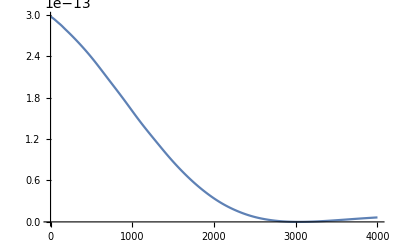

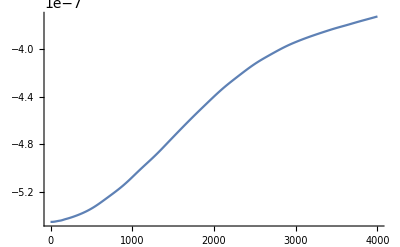

```mathematica
Plot[Evaluate[{ϕ[5.4564×10^(-7)][r]^2}/.sol2],{r,0.0013,4000},PlotRange->All, PlotPoints->200] (*Here, we have plugged in the value of C "guessed" in the integral*)
Plot[Evaluate[{V[5.4564×10^(-7)][r]}/.sol2],{r,0.0035,4000},PlotRange->All, PlotPoints->200]
```

```mathematica
(*Black hole mass = 1.1 × 10^(8) solarmass*)

α3= 41.70 × 10^(-5);
ϵ= -4.7× 10^(-8);

sol3=ParametricNDSolve[{r ϕ''[r]+2ϕ'[r]==2*r*(V[r]-ϵ-α3/r)ϕ[r],r V''[r]+2V'[r]==r ϕ[r]^2,ϕ[0.0417]== C,ϕ'[0.0417]==-3.5×10^(-5)×4.3×10^(-7),V[0.0417]==-C, V'[0.0417]==0},{ϕ,V},{r,0.0417,4000},{C}]
```

{ϕ→ParametricFunction[<>],V→ParametricFunction[<>]}

```mathematica
NIntegrate[Evaluate[4*π*r^2*ϕ[8.00094×10^(-7)][r]^2  /.sol3],{r,0.0417,4000}]
```

0.00494063

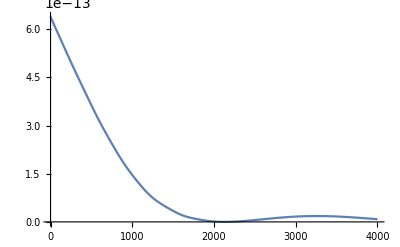

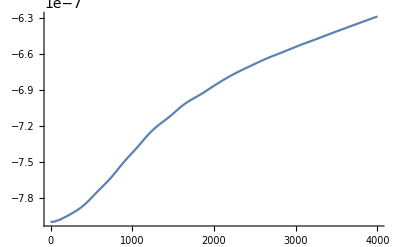

```mathematica
Plot[Evaluate[{ϕ[8.00094×10^(-7)][r]^2}/.sol3],{r,0.0417,4000},PlotRange->All, PlotPoints->200]
Plot[Evaluate[{V[8.00094×10^(-7)][r]}/.sol3],{r,0.0417,4000},PlotRange->All, PlotPoints->200]
```